# The Breadthless Triangle

Euclid opens with two definitions: a point is that which has no part, and a line is breadthless length. A graph has neither. Its points are vertices, and the segment from a to b is the set of all shortest paths between them, the interval I(a,b), which has breadth.

The triangle on three corners a,b,c is the union of the three segments [a,b], [b,c], [c,a]. The vertex density ρ(v) of a segment counts the shortest paths through v; the triangle's density is the sum over its sides.

Let the substrate grow: a tiling at a growing radius, a mesh under refinement. We rescale the path metric and the counting measure so that the circumradius of the triangle stays one. The claim is that the normalized densities ρ_n/∑_v ρ_n(v) converge weakly to the uniform measure on a triangle of the plane, although the support of a side does not thin out at all.

The pictures keep the embedding of the substrate so that the reader sees the plane; no construction below uses it.

## Setup

```mathematica
Needs["WolframInstitute`InfraGeometry`"]
```

The corners: three vertices on the shell of radius r about a centre of the graph, pairwise as far apart as the shell allows. The scale r is half the graph radius.

```mathematica
corners[g_] := With[
  {c = First @ GraphCenter @ g, d = GraphDistanceMatrix @ g},
  {r = Floor[GraphRadius[g]/2]},
  {shell = FindInfraShell[g, c, r]},
  {row = end |-> d[[VertexIndex[g, end], VertexIndex[g, #] & /@ shell]]},
  {a = First @ shell},
  {b = shell[[First @ Ordering[row @ a, -1]]]},
  {a, b, shell[[First @ Ordering[MapThread[Min, {row @ a, row @ b}], -1]]]}]
```

The breadth of a side, read on its level sets: the vertices of the interval at distance t from a, for t=0,…,d(a,b). The breadth of the support is the mean size of a level set, the breadth of the density the mean effective size 1/∑_v p_t(v)^2 of the density normalized on the level set; both in units of the length.

```mathematica
breadth[g_, a_, b_] := With[
  {rho = InfraMeasurement[g, InfraSegment[a, b], "VertexDensity"], d = GraphDistance[g, a]},
  {levels = Values @ GroupBy[Normal @ rho, d[[VertexIndex[g, First @ #]]] & -> Last]},
  {length = Length[levels] - 1},
  {Mean[Length /@ levels] / length, Mean[1 / Total[(# / Total @ #)^2] & /@ levels] / length}]
```

The breadth of a triangle: the mean over its three sides.

```mathematica
triangleBreadth[g_, abc_] := Mean[breadth[g, #1, #2] & @@@ Partition[abc, 2, 1, 1]]
```

## The corners

Each picture below is one substrate at one size: the rows are the sizes small, medium and large, the columns the square tiling, the triangular tiling and an irregular square mesh.

The shell of radius r about the centre is gray, the three corners on it blue. The corners are chosen by the path metric alone, so on the mesh the triangle is as irregular as the mesh is.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {c = First @ GraphCenter @ g},
    {r = Floor[GraphRadius[g]/2]},
    InfraSubstrateHighlight[g, {FindInfraShell[g, c, r] -> StandardGray, corners[g] -> StandardBlue}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

## One side

The side [a,b] is the inert head on the two corners; on a graph it is the interval I(a,b) with its vertex density. The ink is the density: a vertex is drawn the larger and an edge the thicker, the more shortest paths run through it.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {abc = corners @ g},
    InfraSubstrateHighlight[g, {InfraSegment[abc[[1]], abc[[2]]], abc[[;; 2]] -> StandardBlue}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

On the square tiling the interval of two vertices in general position is a full rectangle with the side as its diagonal; the rectangle does not thin out as the tiling grows, but the density concentrates along the diagonal, where the binomial counts of lattice paths peak.

On the triangular tiling a side along a lattice direction is one path; a side off the lattice directions is a parallelogram with the same concentration.

On the mesh a side is a thin bundle of paths, and its density is largest where the bundle is narrowest.

## The density in numbers

The vertex density of the whole triangle, written at each vertex of its support, on the small substrates. A corner carries the paths of both sides through it; a vertex on a thin side carries one.

```mathematica
GraphicsRow @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, "Small", "KeepCoordinates" -> True])},
    {abc = corners @ g},
    {rho = InfraMeasurement[g, InfraUnion @@ (InfraSegment @@@ Partition[abc, 2, 1, 1]), "VertexDensity"]},
    Graph[InfraSubstrateHighlight[g, {InfraSegment @@@ Partition[abc, 2, 1, 1], abc}],
      VertexLabels -> KeyValueMap[#1 -> Placed[#2, Above] &, rho]]],
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

## The triangle

The three sides, each in its own colour, with the corners last; each side is drawn with its own density scale.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {abc = corners @ g},
    InfraSubstrateHighlight[g, Append[InfraSegment @@@ Partition[abc, 2, 1, 1], abc]]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

At every size the picture is a triangle: the sides are bundles of shortest paths that meet only at the corners, and no bundle is mistaken for another.

Growing the substrate thins each bundle relative to its length. On the tilings the limit shape is visible already at the medium size; on the mesh the sides stay crooked, since the path metric of a mesh is not the metric of the plane at any finite refinement.

## The triangle as one object

The union of the three sides is one inert head, and its vertex density is the sum of the three densities. Drawn as one object, the three sides share one density scale.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {abc = corners @ g},
    InfraSubstrateHighlight[g, {InfraUnion @@ (InfraSegment @@@ Partition[abc, 2, 1, 1]), abc -> StandardBlue}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

A side along a lattice direction, or a thin side on the mesh, is one path or a few, while a side in general position carries exponentially many. The sum of the raw counts is therefore dominated by the fattest side, and its normalization converges to that side alone, not to the triangle.

The breadthless triangle is the limit of the sum of the three sides each normalized to mass one. The counts are the measurement; the weights are the observer's choice.

## Breadth

On a tiling the base point does not matter: away from the rim the graph is homogeneous, so one large graph suffices and the radius r of the shell carrying the corners is the growing scale. The mesh refines instead, and is read at the shell of half its graph radius.

Both breadths are in units of the side length, so a breadthless side has breadth zero.

The breadth of the density, the mean over the three sides.

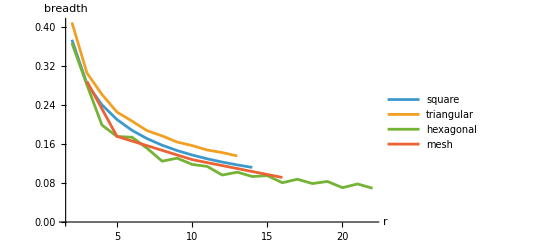

```mathematica
ListLinePlot[
  Join[
    Table[
      With[
        {g = InfraSubstrate[spec[[1]], spec[[2]]]},
        {c = First @ GraphCenter @ g, d = GraphDistanceMatrix @ g},
        Table[
          With[
            {shell = FindInfraShell[g, c, r]},
            {row = end |-> d[[VertexIndex[g, end], VertexIndex[g, #] & /@ shell]]},
            {a = First @ shell},
            {b = shell[[First @ Ordering[row @ a, -1]]]},
            {abc = {a, b, shell[[First @ Ordering[MapThread[Min, {row @ a, row @ b}], -1]]]}},
            {r, Last @ triangleBreadth[g, abc]}],
          {r, 2, spec[[3]]}]],
      {spec, {{"SquareTilingGraph", 30, 14}, {"TriangularTilingGraph", 26, 13}, {"HexagonalTilingGraph", 45, 22}}}],
    {Table[
      With[
        {g = (SeedRandom[2]; InfraSubstrate["SquareMeshGraph", size])},
        {abc = corners @ g},
        {Floor[GraphRadius[g]/2], Last @ triangleBreadth[g, abc]}],
      {size, {"Small", "Medium", "Large", 0.0003}}]}],
  PlotRange -> All, AxesLabel -> {Text["r"], Text["breadth"]},
  PlotLegends -> Text /@ {"square", "triangular", "hexagonal", "mesh"}]
```

The breadth of the density falls on every substrate, the square tiling and the mesh alike. On a lattice the count of shortest paths through a vertex is a product of binomial coefficients, so the density of a rhombus concentrates on a band of the order of the square root of the length around its diagonal, and the breadth falls as the inverse square root.

The hexagonal tiling alternates between two levels with the parity of the radius.

The breadth of the support, the same sides.

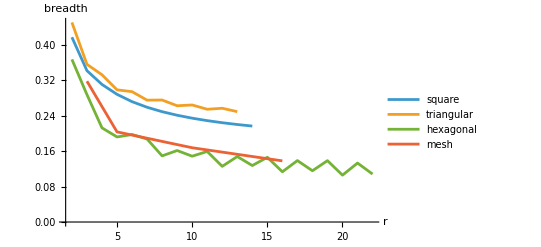

```mathematica
ListLinePlot[
  Join[
    Table[
      With[
        {g = InfraSubstrate[spec[[1]], spec[[2]]]},
        {c = First @ GraphCenter @ g, d = GraphDistanceMatrix @ g},
        Table[
          With[
            {shell = FindInfraShell[g, c, r]},
            {row = end |-> d[[VertexIndex[g, end], VertexIndex[g, #] & /@ shell]]},
            {a = First @ shell},
            {b = shell[[First @ Ordering[row @ a, -1]]]},
            {abc = {a, b, shell[[First @ Ordering[MapThread[Min, {row @ a, row @ b}], -1]]]}},
            {r, First @ triangleBreadth[g, abc]}],
          {r, 2, spec[[3]]}]],
      {spec, {{"SquareTilingGraph", 30, 14}, {"TriangularTilingGraph", 26, 13}, {"HexagonalTilingGraph", 45, 22}}}],
    {Table[
      With[
        {g = (SeedRandom[2]; InfraSubstrate["SquareMeshGraph", size])},
        {abc = corners @ g},
        {Floor[GraphRadius[g]/2], First @ triangleBreadth[g, abc]}],
      {size, {"Small", "Medium", "Large", 0.0003}}]}],
  PlotRange -> All, AxesLabel -> {Text["r"], Text["breadth"]},
  PlotLegends -> Text /@ {"square", "triangular", "hexagonal", "mesh"}]
```

The breadth of the support falls far more slowly than that of the density, and on the tilings not toward zero: the interval of a side in general position is a rhombus, and a rhombus of fixed proportions has a support breadth that does not depend on its length. On the square tiling two of the three sides are such rhombi, with a constant support breadth, and only the third, which runs along the lattice, thins.

On the mesh the support thins slowly, since a mesh has few shortest paths between two vertices to begin with.

The density, not the support, is what converges to Euclid's breadthless line: the triangle emerges as a measure, not as a set.

Related Guides

EuclideanInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/EuclideanInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/BreadthlessTriangleTutorial

### Keywords

triangle

segment

interval

vertex density

union

breadth

weak convergence

Gromov-Hausdorff

tiling

mesh